```mathematica
ClearAll[files,importfile,raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/4 семестр (Оптика)/4.7.2/472.xlsx,/Users/leonidbarinov/Desktop/latexlabs/4 семестр (Оптика)/4.7.2/~$472.xlsx}

```mathematica
importfile=files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/4 семестр (Оптика)/4.7.2/472.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs]
```

## Dataset1

```mathematica
dataset1=makeDataset[raw⟦3⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs=dataset1[All,<|"m"->(#m &),"r"-> (Around[#r, #dr] &)|>]
```

Dataset[<>]

```mathematica
line1 =LinearModelFit[(Normal@dataset1[All,{"m","r"}/*Values]),{0,x},x]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

FittedModel[0.+11.7979 x]

```mathematica
line1["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
0 | 0. | 0. | ComplexInfinity | 0.
x | 11.7979 | 0.452246 | 26.0874 | 1.54644×10^-6

## Dataset2

```mathematica
dataset2=makeDataset[raw⟦4⟧]
```

Dataset[<>]

```mathematica
dataset2WithErrs=dataset2[All,<|"m"->(#m &),"r"-> (Around[#r, #dr] &)|>]
```

Dataset[<>]

```mathematica
line2 =LinearModelFit[(Normal@dataset2[All,{"m","r"}/*Values]),{0,x},x]
```

LinearModelFit::rank: The rank of the design matrix 1 is less than the number of terms 2 in the model. The model and results based upon it may contain significant numerical error.

FittedModel[0.+3.05177 x]

```mathematica
line2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
0 | 0. | 0. | ComplexInfinity | 0.
x | 3.05177 | 0.0231341 | 131.916 | 4.74836×10^-10

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->Black,RoundingRadius->10,FrameMargins->0,Background->White]
```

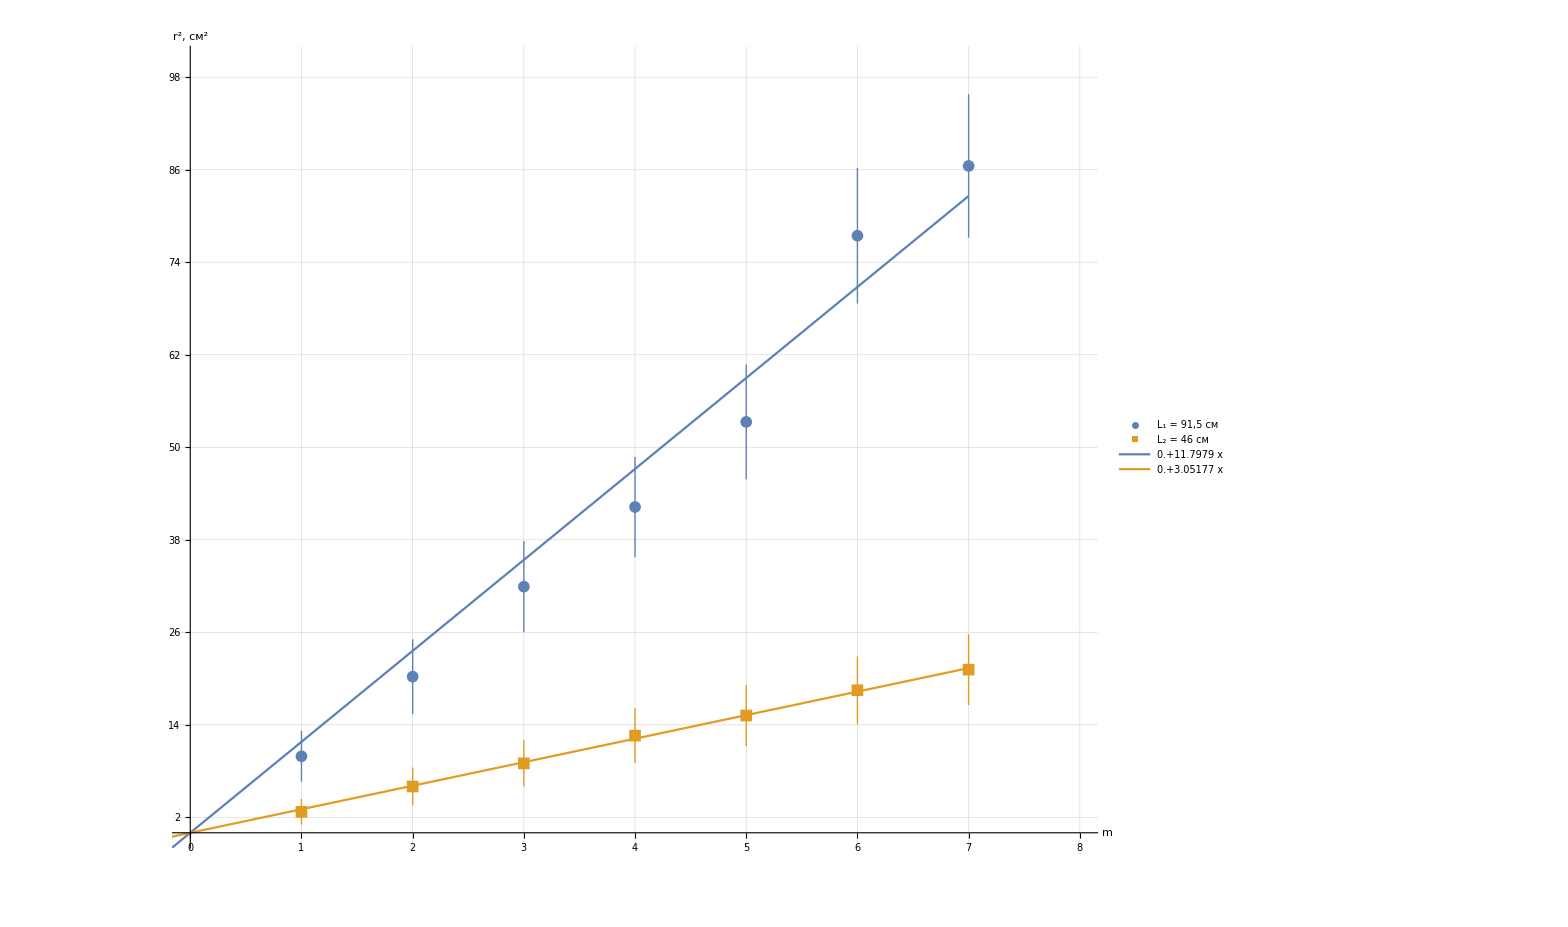

```mathematica
Show[
ListPlot[
{dataset1WithErrs,dataset2WithErrs},
Ticks-> {Range[-5,10,1],Range[-10,1000,4]},
TicksStyle->Directive[Black,14],
PlotMarkers->{Automatic,12},
AxesLabel->{Style["m",Large],Style["r^2, (:0441:043c)^2",Large]},
(*AxesStyle->Directive[Arrowheads[{0.02}],Black], *)
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,

PlotRange->{{0,8},{0,100}},

GridLines->{Range[-5,10,0.25], Range[-10,1000,2]},
LabelStyle->Black,
PlotLegends->Placed[LineLegend[
Automatic,
{"L_1 = 91,5 см","L_2 = 46 см"},
LegendMarkerSize->15,
LegendFunction->frame,
LabelStyle->{FontSize->18},
LegendLayout->"Column"
],
{Scaled[0.2],Scaled[0.75]}
]
],
Plot[
{line1@x,line2@x},
{x,-4, 7},
PlotLegends->Placed[
LineLegend[
{Normal@line1, Normal@line2},
LabelStyle->20,
LegendFunction->frame
],
{Scaled[0.4],Scaled[0.75]}
]
]
]
```